```mathematica
f[T_,H_,m_,Tc_,a0_,u0_]:=w[T]+a[T,Tc,a0]/2 m^2+u[T,Tc,u0]/4 m^4-m*H
w[T_]:=0
a[T_,Tc_,a0_]:=a0*(T-Tc)
u[T_,Tc_,u0_]:=u0
```

```mathematica
χeq[T_,Tc_,a0_,u0_,m_]:=1/(a[T,Tc,a0]+3*u[T,Tc,u0]*m^2)
Heq[T_,Tc_,m_,a0_,u0_]:=a[T,Tc,a0]*m+u[T,Tc,u0]*m^3
meq[T_,Tc_,a0_,u0_]:=Sqrt[-a[T,Tc,a0]/u[T,Tc,u0]]
```

```mathematica
Animate[Plot[{Heq[T,1,m,1,1],If[χeq[T,1,1,1,m]>0,1,-1]},{m,-1.5,1.5},PlotRange->0.6,PlotLabel->T,Filling->{2->Bottom}],{T,0,2,0.1},AnimationRunning->False]
```

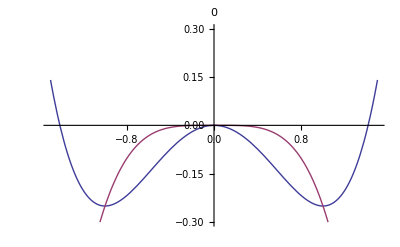
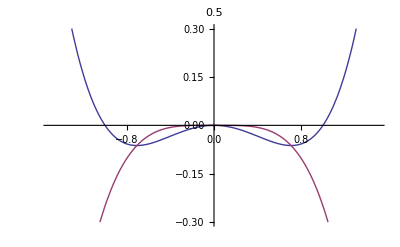
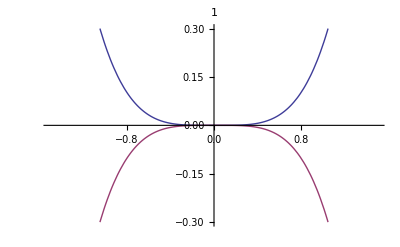
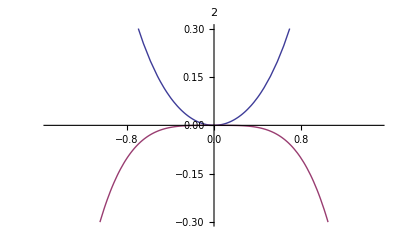

```mathematica
Table[Show[Plot[{f[T,0,m,1,1,1],f[1-1/1*m^2,0,m,1,1,1]},{m,-1.5,1.5},PlotRange->0.3,PlotLabel->T]],{T,{0,0.5,1,2}}]
```

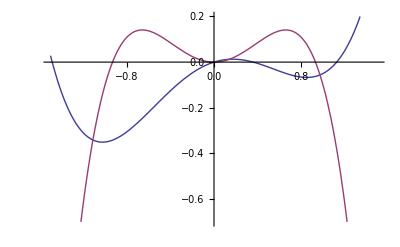
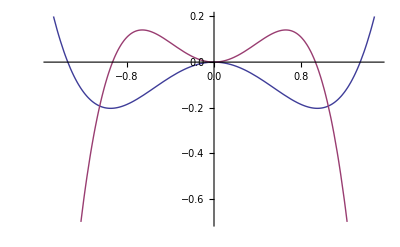
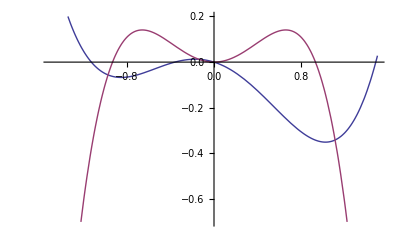

```mathematica
Table[Plot[{f[0.1,H,m,1,1,1],f[0.5,Heq[0.1,1,m,1,1],m,1,1,1]},{m,-1.5,1.5},PlotRange->{-0.7,0.2}],{H,{-0.15,0,0.15}}]
```

```mathematica
f[1-1/1*m^2,0,m,1,1,1]
```

-m^4/4

```mathematica
Expand[f[2,Heq[2,1,m,1,1],m,1,1,1]]
```

-m^2/2-(3 m^4)/4

```mathematica
Plot3D[f[T,Heq[T,1,m,1,1],m,1,1,1],{m,-1.5,1.5},{T,0,2},PlotRange->{-0.3,0.1}]
```

-Graphics3D-

```mathematica
sol=N[Solve[a[T,1.01,1]*m+u [T,1.01,1]*m^3-H==0,m,Reals]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Show[Plot3D[mfazis[T1,H1],{H1,-1,1},{T1,0,1.01},AxesLabel->{"H","T","m"},Exclusions->{H1==0},PerformanceGoal->"Speed"],Plot3D[mfazis[T1,H1],{H1,-1,1},{T1,1.01,2},AxesLabel->{"H","T","m"},PerformanceGoal->"Speed"],PlotRange->All,ViewPoint->{-2,-2,1.5}]
```

Less::nord: Invalid comparison with 0.  - 4.44614×10^-7\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  + 4.44614×10^-7\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  - 4.44614×10^-7\ ⅈ
 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

-Graphics3D-

```mathematica
mfazis[T1_,H1_]:=Evaluate[
If[T1<1,
              If[H1<=0,m/.sol[[1]]/.T->T1/.H->H1,
                  -(m/.sol[[1]])/.T->T1/.H->-H1],
              m/.sol[[1]]/.T->T1/.H->H1
 ]]
```

Less::nord: Invalid comparison with 0.  - 0.379141\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  + 0.379141\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  - 0.379141\ ⅈ
 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

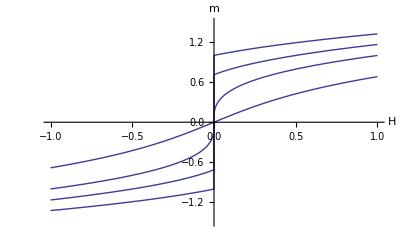

```mathematica
Show[Table[Plot[mfazis[T1,H1],{H1,-1,1},PlotRange->1.5,AxesLabel->{H,m}],{T1,{0,0.5,1,2}}]]
```

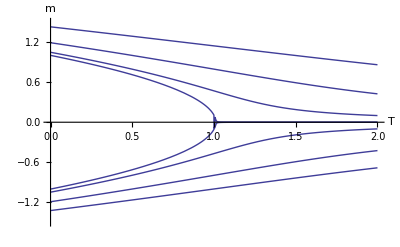

```mathematica
Show[Table[Plot[mfazis[T1,H1],{T1,0,2},PlotRange->1.5,AxesLabel->{T,m}],{H1,{-1,-0.5,-0.1,-0.0001,0.0001,0.1,0.5,1.5}}]]
```

```mathematica
sol2=N[Solve[a[T,1.01,1]*m+u [T,1.01,1]*m^3-H==0,H,Reals]]
```

{{H→-1. (1.01 m-1. m^3-1. m T)}}

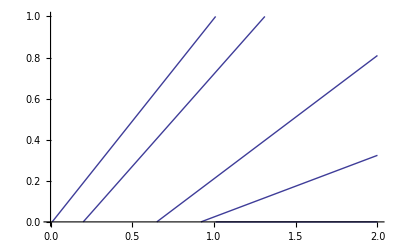

```mathematica
Show[Table[Plot[H/.sol2[[1]]/.T->T1/.m->m1,{T1,0,2},PlotRange->{0,1},PlotStyle->{Thick}],{m1,{0.3,0.6,0.9,1}}],Plot[If[T1>1.01,H/.sol2[[1]]/.T->T1/.m->0],{T1,0,2},PlotRange->{0,1},PlotStyle->{Thick}]]
```

```mathematica
Table[Export["~/Dokumentumok/elsorendu"<>ToString[H2/0.15+1]<>".pdf",Plot[{f[0.1,H2,m,1,1,1]},{m,-1.5,1.5},PlotRange->{-0.7,0.2},PlotStyle->{Thick},AxesLabel->{Style["m",15,Black,FontFamily->"ComputerModern"],Style["F",15,Black,FontFamily->"ComputerModern"]}]],{H2,{-0.15,0,0.15}}]
```

{~/Dokumentumok/elsorendu0..pdf,~/Dokumentumok/elsorendu1..pdf,~/Dokumentumok/elsorendu2..pdf}

```mathematica
For[T2=0,T2≤2,T2++,Export["~/Dokumentumok/masodrendu"<>ToString[T2]<>".pdf",Plot[{f[T,0,m,1,1,1]},{m,-1.5,1.5},PlotRange->0.3,PlotStyle->{Thick},AxesLabel->{Style["m",15,Black,FontFamily->"ComputerModern"],Style["F",15,Black,FontFamily->"ComputerModern"]}]]]
```

```mathematica
Export["~/Dokumentumok/thm.jpg",Show[Plot3D[mfazis[T1,H1],{H1,-1,1},{T1,0,1.01},AxesLabel->{Style["H",15,Black,FontFamily->"ComputerModern"],Style["T",15,Black,FontFamily->"ComputerModern"],Style["m",15,Black,FontFamily->"ComputerModern"]},Exclusions->{H1==0}],Plot3D[mfazis[T1,H1],{H1,-1,1},{T1,1.01,2},AxesLabel->{Style["H",15,Black,FontFamily->"ComputerModern"],Style["T",15,Black,FontFamily->"ComputerModern"],Style["m",15,Black,FontFamily->"ComputerModern"]}],PlotRange->All,ViewPoint->{-2,-2,1.5}],ImageSize->{800,600}]
```

Less::nord: Invalid comparison with 0.  - 2.29127×10^-7\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  + 2.29127×10^-7\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  - 2.29127×10^-7\ ⅈ
 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

~/Dokumentumok/thm.jpg

```mathematica
Export["~/Dokumentumok/HM.pdf",Show[Table[Plot[mfazis[T1,H1],{H1,-1,1},PlotRange->1.5,PlotStyle->{Thick},AxesLabel->{Style["H",15,Black,FontFamily->"ComputerModern"],Style["m",15,Black,FontFamily->"ComputerModern"]}],{T1,{0,0.5,1,2}}]]]
```

Less::nord: Invalid comparison with 0.  - 0.379141\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  + 0.379141\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.  - 0.379141\ ⅈ
 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

~/Dokumentumok/HM.pdf

```mathematica
Export["~/Dokumentumok/TM.pdf",Show[Table[Plot[mfazis[T1,H1],{T1,0,2},PlotRange->1.5,PlotStyle->{Thick},AxesLabel->{Style["T",15,Black,FontFamily->"ComputerModern"],Style["m",15,Black,FontFamily->"ComputerModern"]}],{H1,{-1,-0.5,-0.1,-0.0001,0.0001,0.1,0.5,1.5}}]]]
```

~/Dokumentumok/TM.pdf

```mathematica
Export["~/Dokumentumok/HT.pdf",Show[Table[Plot[H/.sol2[[1]]/.T->T1/.m->m1,{T1,0,2},PlotRange->{0,1},PlotStyle->{Thick},AxesLabel->{Style["T",15,Black,FontFamily->"ComputerModern"],Style["H",15,Black,FontFamily->"ComputerModern"]}],{m1,{0.3,0.6,0.9,1}}],Plot[If[T1>1.01,H/.sol2[[1]]/.T->T1/.m->0],{T1,0,2},PlotRange->{0,1},PlotStyle->{Thick},AxesLabel->{Style["T",15,Black,FontFamily->"ComputerModern"],Style["H",15,Black,FontFamily->"ComputerModern"]}]]]
```

~/Dokumentumok/HT.pdf